## CA Manipulation

```mathematica
initialValues=SparseArray[{{1,1}->1,{2,5}->1,{3,10}->1,{1,6}->1},{5,11}]; (* Define starting values and lattice size. *)
```

```mathematica
initialValues//MatrixForm
```

(1 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)

```mathematica
cellState[cell_,globalState_]:=globalState[[cell[[1]],cell[[2]]]]; (* Returns the value of the cell {x,y}. *)
```

```mathematica
triangularvNN[cell_,lattice_]:=Module[{c1=cell[[1]],c2=cell[[2]]},
If[EvenQ[c2],
{c1,c2}->{{c1,c2-1},{c1,c2},{c1,c2+1},{c1+1,c2-1}},
{c1,c2}->{{c1-1,c2+1},{c1,c2-1},{c1,c2},{c1,c2+1}}
]
]; (* Gives a rule for associating a cell to its von Neumann neighborhood. *)
```

```mathematica
nbhdTable[lattice_]:=Association[Flatten[Table[triangularvNN[{i,j},lattice],{i,1,Dimensions[lattice][[1]]},{j,1,Dimensions[lattice][[2]]}],1]]; (* Associates all cells to their von Neumann neighborhoods. *)
```

```mathematica
vonNeumannNeighborhoods=nbhdTable[initialValues]; (* Evaluate once and use henceforth! *)
```

```mathematica
neighborhoodState[cell_,globalState_]:=Quiet[Module[{n=vonNeumannNeighborhoods[[Key[cell]]]},
Table[If[IntegerQ[cellState[n[[i]],globalState]],cellState[n[[i]],globalState],0],
{i,1,Length[n]}]
]]; (* Returns the state of each cell in the von Neumann neighborhood of the specified cell. *)
```

```mathematica
rules=<|{0,0}->0,{0,1}->1,{0,2}->1,{0,3}->0,{1,1}->0,{1,2}->1,{1,3}->0,{1,4}->0|>; (* An example set of rules. *)
```

```mathematica
cellEvolution[cell_,globalState_]:=Lookup[rules,{{cellState[cell,globalState],Total[neighborhoodState[cell,globalState]]}}][[1]];(* Applies the specified evolution rule to the particular cell. *)
```

```mathematica
globalEvolution[state_]:=SparseArray[{i_,j_}:>cellEvolution[{i,j},state],Dimensions[state]]; (* Applies the specified rule to the current state. *)
```

## CA Graphics

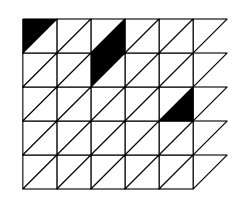
-Graphics-(1 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)

```mathematica
tLatticePlot[basis_,lattice_]:=Module[{b1=basis[[1]],b2={-basis[[2,1]],basis[[2,2]]}},
Table[
If[OddQ[j],
{FaceForm[GrayLevel[1-cellState[{i,j},lattice]]],EdgeForm[Black],Triangle[{b1*((j-1)/2)-b2*(i-1),b1*((j+1)/2)-b2*(i-1),b1*(j-1)/2-b2*(i)}]},
{FaceForm[GrayLevel[1-cellState[{i,j},lattice]]],EdgeForm[Black],Triangle[{b1*(j/2)-b2*(i-1),b1*(j/2-1)-b2*(i),b1*(j/2)-b2*(i)}]}],
{i,1,Dimensions[lattice][[1]]},{j,1,Dimensions[lattice][[2]]}]
];
basis={{1,0},{0,1}};
Row[{Graphics[tLatticePlot[basis,initialValues],ImageSize->50*Dimensions[initialValues][[1]]],initialValues//MatrixForm}]
```

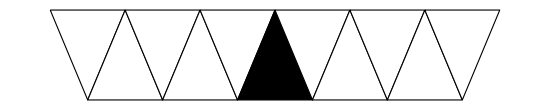

```mathematica
initialValues1D=SparseArray[{1,6}->1,{1,11}];
basis1D={{1,0},{0.5,Sqrt[3]/2}};
tLatticePlot[basis1D,initialValues1D]
```

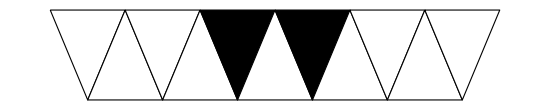

```mathematica
step1=globalEvolution[initialValues1D];
Graphics[tLatticePlot[basis1D,step1]]
```

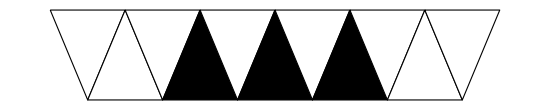
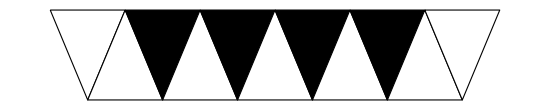
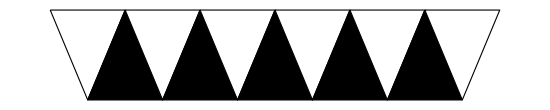
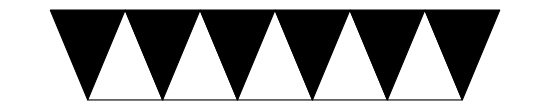
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
c=NestList[globalEvolution[#]&,initialValues1D,7];
tLatticePlot[basis1D,#]&/@c
```

```mathematica
Graphics[NestList[globalEvolution[#]&,initialValues,5]]
```

-Graphics-